# KITTI app

Initialization

```mathematica
SetOptions[ListPlot,PlotStyle->Thick,PlotRange->All,ImageSize->Scaled[0.5]];
```

Data provenant de kittistats

```mathematica
<<"/home/roys/svn3d/imgv/build/out.m"
```

## histoCD

p ( ΔC | correct depth )
ΔC = Abs[  I0[x, y]  -  I1[x - D[x, y], y]   ]
avec D[x,y] le ground truth depth

Cette statistique va nous donner le likelihood
p(correct depth | ΔC) = p( ΔC | depth ) p(depth) / p(ΔC)

```mathematica
sum=Total[histoCD[[All,2]]];
histoCDnorm={#[[1]],#[[2]]/sum}&/@histoCD;
histoCDlog=N[{#[[1]],-Log[10,#[[2]]]}&/@Select[histoCDnorm,(#[[2]]>0)&]];
```

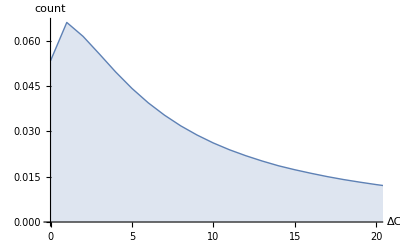

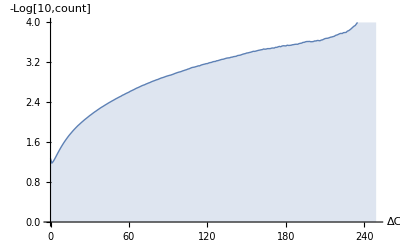

```mathematica
ListPlot[histoCDnorm,Joined->True,Filling->Axis,AxesLabel->{"ΔC","count"},PlotRange->{{0,20},All}]
ListPlot[histoCDlog,Joined->True,Filling->Axis,AxesLabel->{"ΔC","-Log[10,count]"},PlotRange->{All,{0,4}}]
```

```mathematica
(*<<"/home/roys/svn3d/imgv/build/out1.m"*)
```

```mathematica
sum=Total[histoD[[All,2]]]
```

49048061

```mathematica
histoDprob={#[[1]],#[[2]]/sum}&/@histoD;
histoDlog={#[[1]],-Log[10,#[[2]]/sum]}&/@Select[histoD,(#[[2]]>0)&];
```

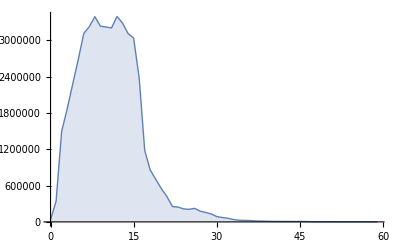

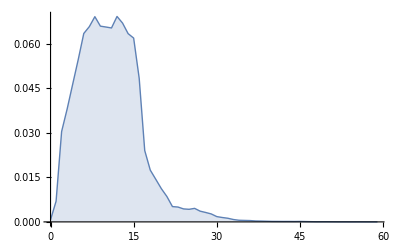

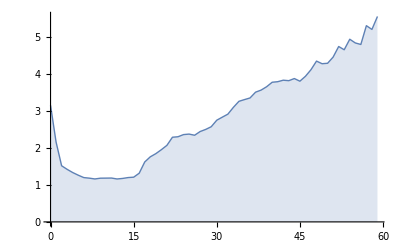

```mathematica
ListPlot[histoD,Joined->True,Filling->Axis]
ListPlot[histoDprob,Joined->True,Filling->Axis]
ListPlot[histoDlog,Joined->True,Filling->Axis]
```

## Lecture HistoLissage binaire

```mathematica
stream=OpenRead["/home/roys/svn3d/imgv/build/histoLissage.data",BinaryFormat->True];
{nbD,nbC,nbP}=BinaryReadList[stream,"Integer32",3]
h0=BinaryReadList[stream,"Integer32"];
Close[stream];
Length[h]
h=Partition[Partition[h0,nbP],nbC];
Dimensions[h]
```

{60,100,300}

60

{60,100,300}

#### Distance general

```mathematica
hh=Flatten[h,{{3},{1,2}}];
Dimensions[hh]
hh=Total/@hh;
hh=hh/Total[hh];
hhL=-Log[10.,hh];
hhuni=1./Length[hh];
hhLuni=-Log[10.,1./Length[hhL]]
```

{300,6000}

2.47712

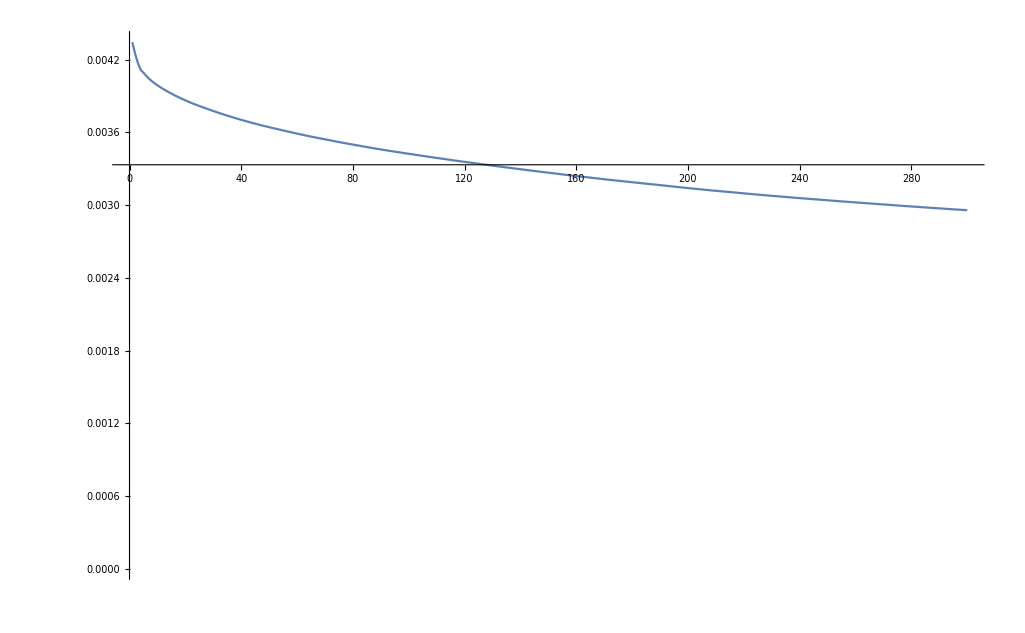

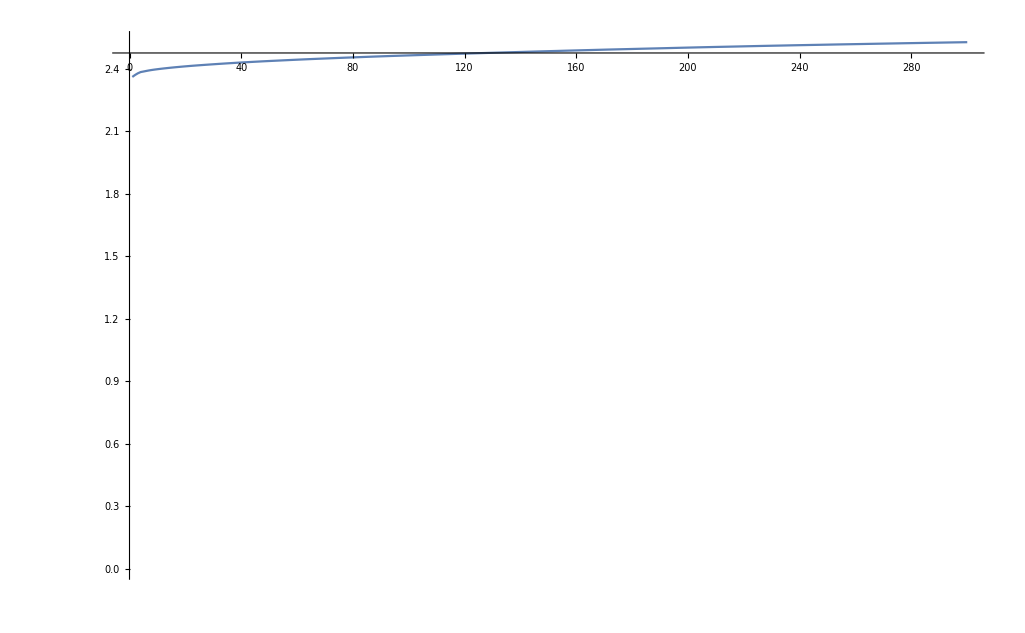

```mathematica
ListPlot[hh,Joined->True,PlotRange->{0,Max[hh]},AxesOrigin->{0,hhuni}]
ListPlot[hhL,Joined->True,PlotRange->{0,Max[hhL]},AxesOrigin->{0,hhLuni}]
```

#### Couleur general

```mathematica
hh=Flatten[h,{{2},{1,3}}];
Dimensions[hh]
hh=Total/@hh;
hh=hh/Total[hh];
hhL=-Log[10.,hh];
hhuni=1./Length[hh];
hhLuni=-Log[10.,1./Length[hhL]]
```

{100,18000}

2.

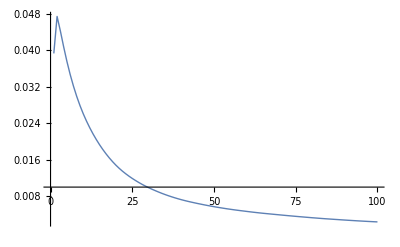
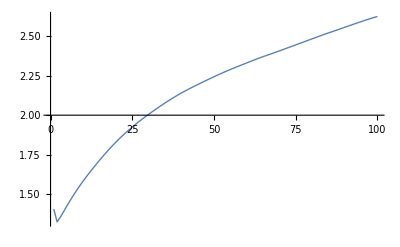

```mathematica
ListPlot[hh,Joined->True,ImageSize->Scaled[0.8],PlotStyle->Thick,PlotRange->All,AxesOrigin->{0,hhuni}]ListPlot[hhL,Joined->True,ImageSize->Scaled[0.8],PlotStyle->Thick,PlotRange->All,AxesOrigin->{0,hhLuni}]
```

#### Depth general

```mathematica
hh=Flatten[h,{{1},{2,3}}];
Dimensions[hh]
hh=Total/@hh;
hh=hh/Total[hh];
hhL=-Log[10.,Select[hh,(#>0)&]];
hhuni=1./Length[hh];
hhLuni=-Log[10.,1./Length[hhL]]
```

{60,30000}

1.77815

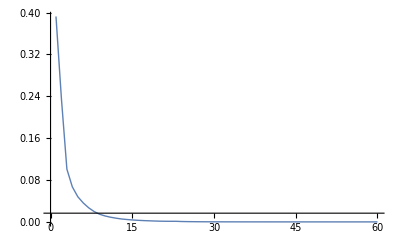
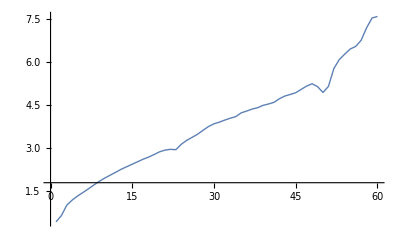

```mathematica
ListPlot[hh,Joined->True,ImageSize->Scaled[0.8],PlotStyle->Thick,PlotRange->All,AxesOrigin->{0,hhuni}]ListPlot[hhL,Joined->True,ImageSize->Scaled[0.8],PlotStyle->Thick,PlotRange->All,AxesOrigin->{0,hhLuni}]
```